Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. 
Departamento: Matemáticas.
F.Javier Muñoz Delgado
Curso 2024/25

# Práctica 1 - Introducción al Mathematica

# Práctica 1. Introducción al Mathematica.

0. Cuestiones previas.

	Al acceder al aula de informática y encender el ordenador hay que registrarse como usuario (queda así constancia de quién ha utilizado cada ordenador y sirve para conocer las asistencias).

	¿Por qué clases de matemáticas en un aula de informática? En muchas ocasiones resolver un problema requiere de dos líneas para contar lo que hay que hacer y dos páginas para realizar los cálculos. Además, al hacer éstos podemos cometer errores y un problema que podríamos tener bien, porque sabemos lo que hay que hacer, está mal. Los problemas que se realizan en clase o se ponen en exámenes están preparados o "trucados" para que los cálculos sean sencillos y los valores de los datos sean números "bonitos". En la realidad esto no suele suceder y los datos reales o experimentales pueden tener muchos dígitos o muchas cifras decimales. 
	Gracias al empleo de software matemático podremos centrarnos en lo importante, en comprender los problemas, los cálculos serán mucho más sencillos y los problemas podrán ser más reales.
	En Educación Primaria aprendimos a sumar, restar, multiplicar o dividir a mano. Con el paso de los cursos, fuimos usando la calculadora para cálculos que tuviesen cierta dificultad. De la misma forma, tras aprender a derivar, integrar, trabajar con matrices y ecuaciones, etc. podríamos usar software matemático para los cálculos de cierta dificultad.
	
	¿Qué software utilizaremos? Utilizaremos el programa Mathematica. Busca el icono en el escritorio. Existen diversas versiones. Las versiones más actuales aceptan documentos elaborados en versiones anteriores.

	¿Por qué el Mathematica? Por ser uno de los más difundidos y con más bibliografía. Las versiones posteriores aceptan lo que se hacía con las anteriores. Por ello, los libros siguen siendo válidos. El uso de las paletas de símbolos ha simplificado la escritura de muchas instrucciones, no obstante pueden darse sin el uso de paletas como en las versiones primeras.

	Con el uso de este programa estarás usando una herramienta actual, podrás dedicar más tiempo a comprender los problemas y menos a realizar cálculos tediosos, podrás ver dibujadas cosas que te ayudarán a comprender las explicaciones, más allá de lo que podrías hacer con la pizarra.

1. Los primeros pasos.

	Al arrancar el programa (por ejemplo, haciendo doble clic sobre el icono, o buscándolo entre los programas en Inicio) abrimos un nuevo documento; una hoja en blanco. Sobre ella escribimos.

	Al comenzar a escribir, observamos que aparece un corchete en la parte derecha de la pantalla, englobando lo que escribimos (se llama celda).

	Quizás sea bueno comenzar dando un título a lo que vamos a realizar. Por ejemplo, podemos escribir "Práctica 1. Introducción al Mathematica". Si pinchamos en el corchete que aparece a la derecha y en Formato (Menú de la barra horizontal superior) elegimos Estilo y Title.

	Después podemos salirnos de esa celda (podemos hacerlo con las flechas, o pinchar con el ratón fuera de la celda) y escribir comentarios (no es necesario tomar apuntes en el papel). En este caso podemos escoger en Formato, Estilo, Text. 

	Cada uno dispone de su propio ordenador. Eso permite que cada uno pueda personalizar sus prácticas, añadiendo los comentarios que estime oportunos y experimentando los cálculos que crea conveniente.

2. ¿Qué podemos hacer con el Mathematica?

	En primer lugar es una gran calculadora y permite hacer las operaciones usuales. En una celda nueva escribe 2+2, fuera de la celdilla anterior de comentarios. Para hacer cálculos, no hay que cambiar de estilo a la celda, por defecto ya tiene el adecuado para los cálculos que es Input.

```mathematica
2+2
```

4

Para obtener el resultado hay que pulsar la tecla Intro (a la derecha y abajo del teclado amplio) o May+Entrar.  Si sólo se pulsa Entrar el cursor salta de línea, continuamos en la misma celda y no se realiza la operación. Tras un breve instante aparece el resultado.

	Observa que aparece el resultado en una nueva celda y que el programa ha numerado con In[1] (de Input, o entrada) la primera de las ordenes y con Out[1] (de salida) el primer resultado. Sucesivamente, el Mathematica continuará numerando lo que escribimos y los cálculos que obtiene.

	Sería bueno guardar el archivo. Si lo hacéis en el Escritorio del ordenador del Aula de Informática, al apagar el ordenador se borrará. Por ello es bueno que traigáis un Pen Drive o que os enviéis por correo electrónico la práctica que hagáis. También es posible guardar el archivo en formato pdf, así podrás verlo en cualquier ordenador, aunque no tenga instalado el programa. 
 
	Si guardas el archivo y cierras el documento, al volver no verás la numeración con los In o los Out, puedes pulsar Intro o May + Entrar e irán apareciendo.

	Continúa practicando, escribe números con muchas cifras o suma varios números a la vez.

```mathematica
23897987 + 332409804983049
```

332409828881036

Parece que el Mathematica trabaja con muchos dígitos.

	De forma similar podemos calcular restas (-), productos (*) o divisiones (/). Para multiplicaciones, también vale dejar un espacio en blanco. Usad paréntesis cuando sea necesario.

	Cada uno tiene su ordenador. Por favor, experimetad.

	Si hacéis algo "mal", el Mathematica suele responder con un mensaje en rojo, en inglés, que debéis tratar de comprender, pues nos puede ayudar para localizar el fallo.

```mathematica
23425534435645645 * 321412423423424124
```

7529257792949740726492926608539980

```mathematica
(24-12)*35 (24-3(23-5))
```

-12600

```mathematica
1/3
```

1/3

1 dividido entre 3 no es 0.3, ni 0.33, ni 0.333, ..., el Mathematica no quiere perder precisión por ello responde que 1 entre 3 es un tercio. Quizás lo que nosotros le pedíamos al ordenador es que diese una aproximación decimal. El Mathematica quiere hacer las cosas con la máxima precisión. Por ello, considera que 0.33333 no es un tercio, sólo es una aproximación.

	Si queremos pedir al Mathematica una aproximación numérica o decimal, podemos usar la primera función que vamos a conocer del Mathematica. La función aproximación numérica decimal, N.

	Todas las funciones del Mathematica comienzan por mayúscula, el resto de la palabra suele ser en minúsculas, salvo palabras compuestas, donde cada trozo comienza por mayúsculas. A lo que se aplica la función, el argumento, debe ir siempre entre corchetes, [ ], no valen paréntesis, llaves, etc.

```mathematica
N[1/3]
```

0.333333

Obtenemos una aproximación de 1/3 con seis cifras significativas. Si queremos más precisión hemos de indicarla, escribiendo una coma tras 1/3 y escribiendo cuántas cifras significativas queremos.

```mathematica
N[1/3,100]
```

0.3333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333

Ahora aparece con 100 cifras significativas. En general, la instrucción N[algo, precisión] da la aproximación numérica de "algo" con un número, "precisión", de cifras significativas. Otra posibilidad es escribir el 1 o el 3 como números reales (no necesariamente enteros), es decir, escribir 1. (el uno y el punto), o 1.0 en lugar de sólo el 1, o 3. en lugar de sólo el tres.

	Cuidado con las mayúsculas y minúsculas. Cuidado con no confundir corchetes, paréntesis, llaves, etc. Ni puntos con comas, etc. El orden de las cosas es importante.

	Podemos trabajar con fracciones

```mathematica
1/3 + 1/6
```

1/2

Para que quede más bonito podemos usar la Paleta. En el Menú de la barra horizontal vemos Paletas, escogemos la primera Asistente de clases (Esto puede cambiar según la versión del Mathematica). Allí pinchamos sobre los símbolos o formatos que necesitamos y así escribimos, por ejemplo, fracciones.

```mathematica
1/2+3/5+8
```

91/10

Con el Mathematica podemos calcular también raíces cuadradas, exponenciales, potencias, logaritmos, senos, cosenos, ...

```mathematica
√9
```

3

Con letras, en lugar de usar la paleta, podemos escribir la función raíz cuadrada de la forma Sqrt y entre corchetes el número.

```mathematica
Sqrt[4]
```

2

```mathematica
√2
```

√2

¿No calcula la raíz de 2? Otra vez el problema con la precisión. Usemos la función N.

```mathematica
N[√2]
```

1.41421

si queremos más cifras

```mathematica
N[√2,120]
```

1.41421356237309504880168872420969807856967187537694807317667973799073247846210703885038753432764157273501384623091229702

o escribir

```mathematica
Sqrt[2.]
```

1.41421

Para escribir la base y el exponente podemos usar la paleta.

```mathematica
2^125
```

42535295865117307932921825928971026432

La exponencial se haría con la letra E o con la ⅇ que encontramos en la paleta.

```mathematica
ⅇ^3
```

ⅇ^3

```mathematica
N[ⅇ^3,12]
```

20.085536923

Las potencias también se pueden escribir con el acento ^, o utilizando la paleta. Cada uno puede hacerlo como le sea más cómodo.

```mathematica
2^23
```

8388608

El coseno se escribe Cos, el seno Sin, la tangente Tan. Siempre se refiere a ángulos en radianes. El número π, se puede escribir con la paleta o de la forma Pi.

```mathematica
Cos[0]
```

1

```mathematica
Cos[Pi]
```

-1

```mathematica
Cos[π/2]
```

0

```mathematica
Sin[π/2]
```

1

Recordad: Siempre trabajamos en radianes.

	El logaritmo neperiano, natural o en base ⅇ, es Log. No es normal que en este curso trabajemos en otras bases.

```mathematica
Log[ⅇ]
```

1

```mathematica
N[Log[5],27]
```

1.60943791243410037460075933

Este programa permite trabajar con números, pero también con "letras".

```mathematica
a+a
```

2 a

```mathematica
a+7a
```

8 a

7a, 7*a, 7 a (este último dejando un espacio en blanco) son tres formas distintas de poner que 7 multiplica a “a”. Pero no vale escribir a7 (sin el espacio en blanco, no entiende que se estén multiplicando, sino que hay algo que se llama a7)

```mathematica
3*a+7a + a4
```

10 a+a4

```mathematica
(3 a + 7 a) a-2a^2
```

8 a^2

```mathematica
20 kilos * 30 euros/kilos
```

600 euros

Cuando las letras (y en su caso números) van sin espacio el programa entiende que no se están multiplicando sino que forman una palabra. Sólo cuando un número va seguido de letras se entiende que se multiplican. Si escribimos 2b (sin espacios) el programa entenderá dos veces b, en cambio si escribimos b2 el ordenador entenderá que es algo llamado así.

	Si queremos calcular expresiones

```mathematica
(a+b)^2
```

(a+b)^2

Claro que podemos preferir que la desarrolle, eso se hace con la función Expand.

```mathematica
Expand[(a+b)^2]
```

a^2+2 a b+b^2

```mathematica
Expand[(a+7b)^20]
```

a^20+140 a^19 b+9310 a^18 b^2+391020 a^17 b^3+11632845 a^16 b^4+260575728 a^15 b^5+4560075240 a^14 b^6+63841053360 a^13 b^7+726191981970 a^12 b^8+6777791831720 a^11 b^9+52188997104244 a^10 b^10+332111799754280 a^9 b^11+1743586948709970 a^8 b^12+7510836086750640 a^7 b^13+26287926303627240 a^6 b^14+73606193650156272 a^5 b^15+161013548609716845 a^4 b^16+265198785945415980 a^3 b^17+309398583602985310 a^2 b^18+227977903707462860 a b^19+79792266297612001 b^20

Al contrario podemos trabajar con la función Simplify

```mathematica
Simplify[a^2 + 2 a b + b^2]
```

(a+b)^2

¿Qué más cosas hacíamos en el colegio o instituto? Resolver ecuaciones, dibujar gráficas de funciones, derivadas, integrales, ...matrices, determinantes, ..

Podemos resolver ecuaciones con la función Solve. Hay que escribir la ecuación usando doble igual y especificando después la incógnita (podríamos tener parámetros y es necesario especificar)

```mathematica
Solve[2x+1==9,x]
```

{{x→4}}

```mathematica
Solve[2x+1==8x-3x^2+2,x]
```

{{x→1/3 (3-2 √3)},{x→1/3 (3+2 √3)}}

En la ecuación podrían aparecer diversas incógnitas o parámetros, debemos por tanto, indicarle a Mathematica qué queremos calcular, o despejar.

```mathematica
Solve[2x+y==7,x]
```

{{x→(7-y)/2}}

```mathematica
Solve[2x+y==7,y]
```

{{y→7-2 x}}

En cada caso, el resultado y la dificultad del problema puede ser muy distinto.

Para resolver sistemas de ecuaciones con varias incógnitas tenemos que escribir todas las ecuaciones entre llaves y todas las incógnitas entre llaves. Por ejemplo,

```mathematica
Solve[{3x+2y==7, 2x-y==3},{x,y}]
```

{{x→13/7,y→5/7}}

También se puede utilizar la instrucción Reduce.

```mathematica
Reduce[{3x+2y==7, 2x-y==3},{x,y}]
```

x==13/7&&y==5/7

También se puede trabajar con inecuaciones.

```mathematica
Reduce[2x+3≤ x,x]
```

x≤-3

Para dibujar gráficas de funciones reales de una variable real con la función Plot. Hay que especificar el intervalo en el que queremos la gráfica, entre llaves escribimos la variable, el extremo inferior y el superior del intervalo donde queremos dibujar,

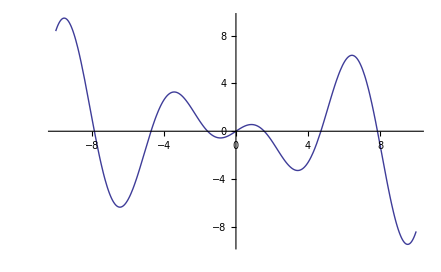

```mathematica
Plot[x Cos[x],{x,-10,10}]
```

Si queremos comparar varias gráficas podemos dibujarlas de forma simultánea.

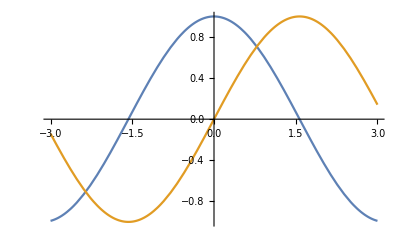

```mathematica
Plot[{Cos[x],Sin[x]},{x,-3,3}]
```

En el menú superior horizontal podemos escoger Ayuda y seleccionar Documentación Wolfram. Allí podemos buscar Plot y conocer más sobre esta función (o cualquier otra) y buscar diversas opciones. Como podéis comprobar hay miles de instrucciones o funciones. Nuestro objetivo es usar el Mathematica y aprender Análisis y Métodos Numéricos utilizando (memorizando) el mínimo número de funciones.

También podemos definir nuestras propias funciones. Para ello nos inventamos un nombre que no puede ser uno de los que ya usa el Mathematica (estos se saben desde la versión 6.0 porque al escribirlos se ponen de color negro). Podemos usar mayúsculas y minúsculas e incluir cifras (aunque no como inicial). Después hay que colocar un guión bajo tras la variable y poner dos puntos antes del igual.

```mathematica
f[x_]:= 2x Cos[x^2]
```

Al pulsar Intro en la celda donde hemos definido la función f, el Mathematica lo almacena en su memoria (aunque sólo temporalmente, al salir del programa se borrará). No aparece salida alguna, es decir, no veremos Out[ ]. Al memorizar la función, color de f cambiará de azul a negro. Ahora podemos evaluar, derivar, integrar, representar, ... nuestra función.

```mathematica
f[0]
```

0

```mathematica
f[x]
```

2 x Cos[x^2]

```mathematica
f'[x]
```

2 Cos[x^2]-4 x^2 Sin[x^2]

```mathematica
f''[x]
```

-8 x^3 Cos[x^2]-12 x Sin[x^2]

```mathematica
f'''[x]
```

-48 x^2 Cos[x^2]-12 Sin[x^2]+16 x^4 Sin[x^2]

Si queremos derivadas de más alto orden es más cómodo usar la función D y especificar el orden de la derivada que deseamos.

```mathematica
D[f[x],{x,9}]
```

18 (1680 Cos[x^2]-13440 x^4 Cos[x^2]+256 x^8 Cos[x^2]-13440 x^2 Sin[x^2]+3584 x^6 Sin[x^2])+2 x (-80640 x^3 Cos[x^2]+9216 x^7 Cos[x^2]-30240 x Sin[x^2]+48384 x^5 Sin[x^2]-512 x^9 Sin[x^2])

Para integrar podemos usar la paleta.

```mathematica
∫f[x]ⅆx
```

Sin[x^2]

```mathematica
∫_2^4 f[x]ⅆx
```

-Sin[4]+Sin[16]

También se puede utilizar el comando Integrate, tanto para integrales definidas como para calcular primitivas.

```mathematica
Integrate[f[x],x]
```

Sin[x^2]

```mathematica
Integrate[f[x],{x,0,π}]
```

Sin[π^2]

Tipos de funciones que utilizaremos y cómo hacer dibujos asociados.
Durante el curso trabajaremos con funciones de distintos tipos:

f: R⟶R (Funciones reales de una variable). Dibujamos las gráficas. El comando es Plot

f: R^2⟶R (Funciones reales de dos variables). Dibujamos las gráficas. El comando es Plot3D

f: R⟶R^2 (curvas planas). Dibujamos el conjunto de puntos imagen. El comando es ParametricPlot.

f: R⟶R^3 (curvas en el espacio). Dibujamos el conjunto de puntos imagen. El comando es ParametricPlot3D. Usamos sólo un parámetro.

f: R^2⟶R^3 (curvas planas). Dibujamos el conjunto de puntos imagen. El comando es ParametricPlot3D. Usamos dos parámetros.

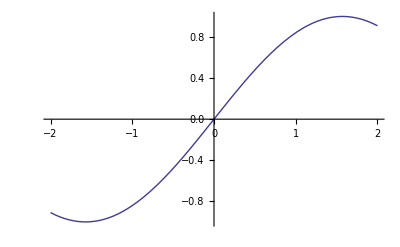

```mathematica
Plot[Sin[x],{x,-2,2}]
```

```mathematica
Plot3D[Cos[x^2+y^2],{x,-3,3},{y,-3,3}]
```

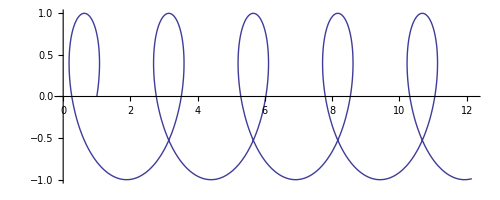

```mathematica
ParametricPlot[{Cos[t]+0.4t,Sin[t]},{t,0,30}]
```

```mathematica
ParametricPlot3D[{t Cos[t],t Sin[t],t},{t,0,20}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t] Sin[s], Sin[t] Sin[s], Cos[s]},{t,0,2Pi},{s,0,Pi}]
```

-Graphics3D-

El Mathematica también trabaja con matrices. En la paleta, en las opciones avanzadas habréis visto el símbolo de una matriz. Aunque en principio es de tamaño 2x2, se pueden ampliar las filas o columnas con las opciones que aparecen en la paleta o con Control+ ,(coma) o con Control + Enter. Podemos hacer operaciones con matrices: sumas, restas o productos, y calcular determinantes o matrices inversas.

```mathematica
Det[({{2, 1}, {3, 5}})]
```

7

```mathematica
Inverse[({{2, 1}, {3, 5}})]
```

{{5/7,-1/7},{-3/7,2/7}}

Una matriz en el Mathematica es una fila de filas. Si queremos que escriba la matriz en forma rectangular podemos utilizar la función MatrixForm.

```mathematica
Inverse[({{2, 1}, {3, 5}})]//MatrixForm
```

(5/7 | -1/7
-3/7 | 2/7)

```mathematica
MatrixForm[({{2, 1}, {3, 5}})+({{3, 8}, {1, 7}})]
```

(5 | 9
4 | 12)

Con el Mathematica también podéis hacer pequeños programas. Instrucciones como For, Do, If, While, ...  nos permitirán programar ciertos algoritmos para trabajar especialmente los métodos numéricos.

Ahora debéis practicar por vuestra cuenta y podéis hacer algunos ejercicios, inventados o propuestos.